# First Steps with the REAP Package

See the 'First Steps' section in the documentation for explanations.

```mathematica
If[$VersionNumber<6,
Get["Graphics`FilledPlot`"];
Get["Graphics`Colors`"],
ForestGreen=RGBColor[0.1,0.75,0.2];
];
```

```mathematica
Needs["REAP`RGEMSSM`"]
```

Loading REAP 1.11

SM0N: Two loop RG equation of κ not implemented yet.

SM: Two loop RG equations of Yν, Mνr and κ not implemented yet.

```mathematica
RGEReset[];
```

```mathematica
RGEAdd["MSSM"]
```

```mathematica
RGESetInitial[2*10^16,RGEYν->{{1,0,0},{0,0.5,0},{0,0,0.1}}]
```

```mathematica
RGESolve[100,2*10^16]
```

```mathematica
MatrixForm[RGEGetSolution[100,RGEMν]]
```

(0.0153556+0. ⅈ | 0.000775493+0. ⅈ | -0.000766466+0. ⅈ
0.000775493+0. ⅈ | 0.0340507+0. ⅈ | 0.0164111+0. ⅈ
-0.000766466+0. ⅈ | 0.0164111+0. ⅈ | 0.0325141+0. ⅈ)

```mathematica
MNSParameters[RGEGetSolution[100,RGEMν],RGEGetSolution[100,RGEYe]]
```

{{0.48449,0.00102627,0.808926,0.,3.14159,0.,0.,0.,0.},{0.014782,0.0174268,0.0497115},{0.000118154,0.0251542,0.395699}}

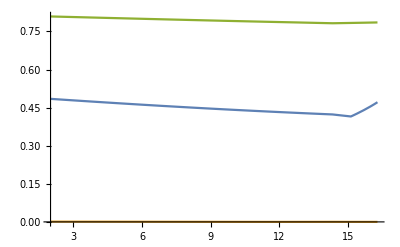

```mathematica
mNu[x_]:=RGEGetSolution[x,RGEMν]
Ye[x_]:=RGEGetSolution[x,RGEYe]
θ12[x_]:=MNSParameters[mNu[x],Ye[x]][[1,1]]
θ13[x_]:=MNSParameters[mNu[x],Ye[x]][[1,2]]
θ23[x_]:=MNSParameters[mNu[x],Ye[x]][[1,3]]
Plot[{θ12[10^x],θ13[10^x],θ23[10^x]},{x,Log[10,100],Log[10,2*10^16]}]
```

Nicer plots can be produced using the notebook RGEPlots.nb in the same directory.

## A Second Run with some Modifications

```mathematica
RGESetOptions["MSSM",RGEtanβ->20]
```

```mathematica
RGEAdd["SM",RGECutoff->200]
```

```mathematica
RGESetInitial[2*10^16,RGEYν->{{1,0,0},{0,0.5,0},{0,0,0.1}},
RGEθ13->6 Degree,RGEφ1->50 Degree,RGEφ2->120 Degree]
```

```mathematica
RGESolve[100,2*10^16]
```

(-0.0144692+1.73757×10^-16 ⅈ | -2.35071×10^-9-1.64362×10^-10 ⅈ | -5.81726×10^-9+1.25486×10^-9 ⅈ
-2.35071×10^-9-1.64362×10^-10 ⅈ | -0.0173049+3.44022×10^-15 ⅈ | -9.3667×10^-9+7.69582×10^-9 ⅈ
-5.81726×10^-9+1.25486×10^-9 ⅈ | -9.3667×10^-9+7.69582×10^-9 ⅈ | -0.049554-1.25156×10^-15 ⅈ)

{{0.44219,0.103004,0.785278,6.22118,3.0876,5.58926,4.18197,0.784692,2.07408},{0.0144692,0.0173049,0.049554},{2.61627×10^-6,0.000557357,0.00942664}}

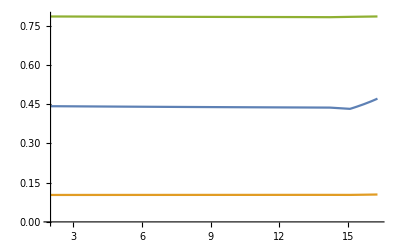

```mathematica
MatrixForm[RGEGetSolution[100,RGEMν]]
MNSParameters[RGEGetSolution[100,RGEMν],RGEGetSolution[100,RGEYe]]

mNu[x_]:=RGEGetSolution[x,RGEMν]
Ye[x_]:=RGEGetSolution[x,RGEYe]
θ12[x_]:=MNSParameters[mNu[x],Ye[x]][[1,1]]
θ13[x_]:=MNSParameters[mNu[x],Ye[x]][[1,2]]
θ23[x_]:=MNSParameters[mNu[x],Ye[x]][[1,3]]
Plot[{θ12[10^x],θ13[10^x],θ23[10^x]},{x,Log[10,100],Log[10,2*10^16]}]
```

## In order to give another example, we define the initial values at the Z-boson mass and determine the renormalization group evolution below the see-saw scales.

At first, we have to go back to the default values.

```mathematica
RGEReset[]
```

Then, the model is defined as:

```mathematica
RGEAdd["MSSM0N"]
RGEAdd["SM0N",RGECutoff->200]
```

and the initial values are set to their default values for simplicity, which can be seen by RGEGetInitial[].

```mathematica
RGESetInitial[91.19,RGESuggestion->"MZ"]
```

```mathematica
RGEGetInitial[]
```

{91.19,{RGEg1→0.461425,RGEg2→0.65184,RGEg3→1.2143,RGEYu→{{7.4×10^-6,0,0},{0,0.0036,0},{0,0,0.9861}},RGEYd→{{0.0000310648+0. ⅈ,0.0000658754-2.34193×10^-6 ⅈ,0.0000183776-0.0000556215 ⅈ},{0.0000658754+2.34193×10^-6 ⅈ,0.000325424+0. ⅈ,0.000676303+2.2135×10^-7 ⅈ},{0.0000183776+0.0000556215 ⅈ,0.000676303-2.2135×10^-7 ⅈ,0.0163613+1.70606×10^-24 ⅈ}},RGEYe→{{2.79475×10^-6,0,0},{0,0.000589986,0},{0,0,0.0100295}},RGEκ→{{-3.32822×10^-15+6.656×10^-17 ⅈ,-1.43792×10^-16+2.58699×10^-16 ⅈ,-1.29441×10^-16+2.93436×10^-16 ⅈ},{-1.43792×10^-16+2.58699×10^-16 ⅈ,-3.89775×10^-15-1.95789×10^-17 ⅈ,-6.37191×10^-16-2.33233×10^-17 ⅈ},{-1.29441×10^-16+2.93436×10^-16 ⅈ,-6.37191×10^-16-2.33233×10^-17 ⅈ,-4.06527×10^-15-2.77203×10^-17 ⅈ}},RGEλ→0.522091}}

```mathematica
RGESolve[91.19,10^10]
```

(0.0503527-0.00100699 ⅈ | 0.00217543-0.00391385 ⅈ | 0.00195831-0.00443939 ⅈ
0.00217543-0.00391385 ⅈ | 0.0589691+0.000296209 ⅈ | 0.00964006+0.000352858 ⅈ
0.00195831-0.00443939 ⅈ | 0.00964006+0.000352858 ⅈ | 0.0615035+0.00041938 ⅈ)

{{0.585907,0.152716,0.722566,5.95157,6.28319,6.28319,6.28319,6.28319,6.28319},{0.05,0.0507395,0.0706789},{2.79475×10^-6,0.000589986,0.0100295}}

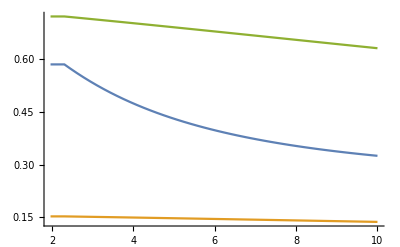

```mathematica
MatrixForm[RGEGetSolution[91.19,RGEMν]]
MNSParameters[RGEGetSolution[91.19,RGEMν],RGEGetSolution[91.19,RGEYe]]

mNu[x_]:=RGEGetSolution[x,RGEMν]
Ye[x_]:=RGEGetSolution[x,RGEYe]
θ12[x_]:=MNSParameters[mNu[x],Ye[x]][[1,1]]
θ13[x_]:=MNSParameters[mNu[x],Ye[x]][[1,2]]
θ23[x_]:=MNSParameters[mNu[x],Ye[x]][[1,3]]
Plot[{θ12[10^x],θ13[10^x],θ23[10^x]},{x,Log[10,91.19],Log[10,10^10]}]
```